```mathematica
Needs["dsvsolve`"];
```

## Input

Edit or simply evaluate the following cell to see the input

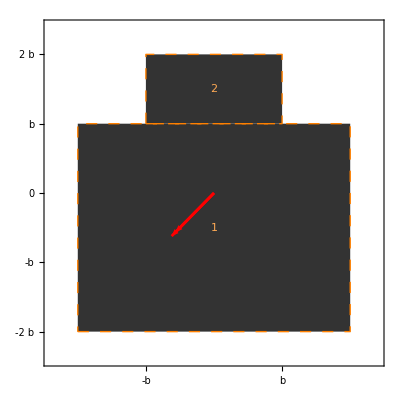

```mathematica
γ=Pi/4;
example={$$domains->{{-2*b, -2*b, 2*b, b}, {-b, b, b, 2*b}},
$$coefficients->{1, 1},
$$traction->0,$$wheretraction->{0, 0},
$$bending->{-MM*Cos[γ], -MM*Sin[γ]}}; dSVcShowInput[example]
```

## Risultati simbolici

```mathematica
A=14b ^2;xG=0;yG=(3 b)/14;Iη=(50 b^4)/3;Iξ=(673 b^4)/42;a0=-(9 MM)/(673 √2 b^3);a1=(3 MM)/(50 √2 b^4);a2=-(21 √2 MM)/(673 b^4);σ[x_,y_]=a0-a1 x-a2 y;tanβ=-a1/a2;β=ArcTan[tanβ];σmax=σ[2*b,-b];σmin=σ[-2 *b,2*b];
```

## Risultati numerici

```mathematica
valori1={γ->45*Pi/180,MM->Quantity[4*10^4,"Kilonewtons"*"Centimeters"],b->Quantity[10,"Centimeters"],σ0->Quantity[20,"Kilonewtons"/"Centimeters"^2]};
risultati1={A,Iξ,Iη,β*180/Pi,σmax,σmin,σmax/σ0,σmin/σ0}/.valori1//N//NumberForm[#,3]&
```

NumberForm::reqsigz: Requested number precision is lower than number of digits shown; padding with zeros.

General::stop: Further output of NumberForm::reqsigz will be suppressed during this calculation.

{1400. cm^2,160000. cm^4,167000. cm^4,43.9,-5.54 kN/cm^2,6.55 kN/cm^2,-0.277,0.327}

## Output

Evaluate the following cell to solve the problem and see the output

```mathematica
sol = {AB, rG, JB, sigma, gobj, details} = dSVcSolve[example];
gsol=dSVcShowOutput[example, sol]
```

First::nofirst: {} has zero length and no first element.

Last::nolast: {} has zero length and no last element.

123456

Evaluate the following cell to print the above output

```mathematica
CellPrint/@Rest/@Last[sol];
Print/@Cases[gsol,Graphics[___],Infinity];
```

Numerical assumptions for visualization purposes

{b→0.75,MM→0.94}

Areas of elementary domains Ai

{{12 b^2,2 b^2}}

Total Area A

14 b^2

Static moments of elementary domains sPi

{{{0,-6 b^3},{0,3 b^3}}}

Total static moment sP

{{0,-3 b^3}}

Centroids of elementary domains Gi

{{{0,-b/2},{0,(3 b)/2}}}

Centroid G

{{0,-(3 b)/14}}

Euler inertia tensors of elementary domains IPi

{{{{16 b^4,0},{0,12 b^4}},{{(2 b^4)/3,0},{0,(14 b^4)/3}}}}

Total Euler inertia tensor IP

{{(50 b^4)/3,0},{0,(50 b^4)/3}}

Inertia tensor after translation in the centroid IG

{{(50 b^4)/3,0},{0,(673 b^4)/42}}

Principal inertia momoments (jI, jII) and associated directions

{{(673 b^4)/42,{1,0}},{(50 b^4)/3,{0,1}}}

Rotation to principal directions

0

Radii of gyration (ρI, ρII)

{{1/14 √(673/3) b,(5 b)/(√21)}}

Section moduli (WI, WII) and associated directions

{{{(673 b^3)/75,(673 b^3)/93},{1,0}},{{(25 b^3)/3,(25 b^3)/3},{0,1}}}

Coefficients {a0,a1,a2} for sigma (= a0 + a1 x1 + a2 x2)

{-(9 MM)/(673 √2 b^3),(3 MM)/(50 √2 b^4),-(21 √2 MM)/(673 b^4)}

Sigma in principal axis (ξ,η)

(-0.0441285 "η" MM+0.0424264 "ξ" MM)/b^4

Neutral axis

{x2→-(3 b)/14+(673 x1)/700}

Intersections of neutral axis with principal axis

{Last[{}],Last[{}]}

Inertia ellipse equation

21 (673 x1^2+100 x2 (3 b+7 x2))==32975 b^2

Sigma values in relevant points

{{{-b,2 b},-(6669 MM)/(33650 √2 b^3)},{{-b,b},-(4569 MM)/(33650 √2 b^3)},{{b,2 b},-(2631 MM)/(33650 √2 b^3)},{{b,b},-(531 MM)/(33650 √2 b^3)},{{-2 b,b},-(1647 √2 MM)/(16825 b^3)},{{-2 b,-2 b},-(72 √2 MM)/(16825 b^3)},{{2 b,b},(372 √2 MM)/(16825 b^3)},{{2 b,-2 b},(1947 √2 MM)/(16825 b^3)}}

Kern (convex hull has been computed on a numerical instance!)

{{-(25 b)/42,-(3 b)/14},{-(10 b)/27,-(77 b)/135},{0,-(68 b)/93},{(10 b)/27,-(77 b)/135},{(25 b)/42,-(3 b)/14},{0,(32 b)/75}}

-Graphics-

-Graphics-